# Dormand p63

```mathematica
TMax=6.192169331319640;
m=1/82.45;e=1-m;
{xSol,ySol}=NDSolveValue[{
r1=√((x[t]+m)^2+y[t]^2); r2=√((x[t]-e)^2+y[t]^2);
x''[t]==2 y'[t] +x[t] - (e(x[t]+m))/r1^3-(m(x[t]-e))/r2^3,
y''[t]==-2 x'[t] +y[t] - (e(y[t]))/r1^3-(m(y[t]))/r2^3,
x[0]==1.2,y'[0]==-1.049357509830320,y[0]==0,x'[0]==0
},
{x,y},
{t,0, TMax}
];
TabView[{
"x & y vs t"->Plot[{xSol[t],ySol[t]},{t,0, TMax},PlotLegends->{"x","y"}],
"xy"->ParametricPlot[{xSol[t],ySol[t]},{t,0,TMax}]}]
```

12

```mathematica
{rOrbit, rEarth, rMoon}={238,4,4};
Manipulate[Graphics[{
{LightGreen, Disk[{0,0},rOrbit]},
{Blue,Disk[({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}).{-m rOrbit,0},rEarth]},
{Red, Point[{0,0}]},
{PointSize[0.01],Point[rOrbit*({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}).{xSol[t],ySol[t]}]},
{Green,Disk[({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}).{e rOrbit,0},rMoon]}
},PlotRange->1.5*rOrbit*{{-1,1},{-1,1}}],{t, 0,TMax}]
```

InterpolatingFunction[…]

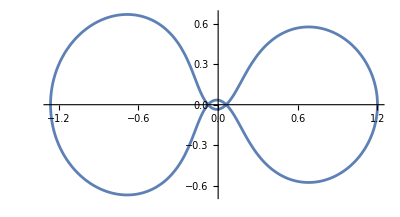

```mathematica
f[{m_,e_}][{x_,vx_,y_,vy_}]:=Module[{r1,r2},
r1=√((x+m)^2+y^2); r2=√((x-e)^2+y^2);
{vx,2 vy +x - (e(x+m))/r1^3-(m(x-e))/r2^3,
vy,-2 vx +y - (e(y))/r1^3-(m(y))/r2^3}
]
m=1/82.45;e=1-m;
u0={1.2,0,0,-1.049357509830320};
TMax=6.192169331319640;
uSol=NDSolveValue[{u'[t]==f[{m,e}][u[t]],u[0]==u0},u,{t, 0, TMax}]
ParametricPlot[uSol[t]⟦{1,3}⟧,{t,0, TMax}]
```

The Dormand book says that he

```mathematica
MatrixForm[
D[f[{m,e}][{x,vx,y,vy}],{{x,vx,y,vy}}]
]
```

(0 | 1 | 0 | 0
1+(0.0363857 (-0.987871+x)^2)/(((-0.987871+x)^2+y^2)^(5/2))-0.0121286/(((-0.987871+x)^2+y^2)^(3/2))+(2.96361 (0.0121286+x)^2)/(((0.0121286+x)^2+y^2)^(5/2))-0.987871/(((0.0121286+x)^2+y^2)^(3/2)) | 0 | (0.0363857 (-0.987871+x) y)/(((-0.987871+x)^2+y^2)^(5/2))+(2.96361 (0.0121286+x) y)/(((0.0121286+x)^2+y^2)^(5/2)) | 2
0 | 0 | 0 | 1
(0.0363857 (-0.987871+x) y)/(((-0.987871+x)^2+y^2)^(5/2))+(2.96361 (0.0121286+x) y)/(((0.0121286+x)^2+y^2)^(5/2)) | -2 | 1+(0.0363857 y^2)/(((-0.987871+x)^2+y^2)^(5/2))-0.0121286/(((-0.987871+x)^2+y^2)^(3/2))+(2.96361 y^2)/(((0.0121286+x)^2+y^2)^(5/2))-0.987871/(((0.0121286+x)^2+y^2)^(3/2)) | 0)